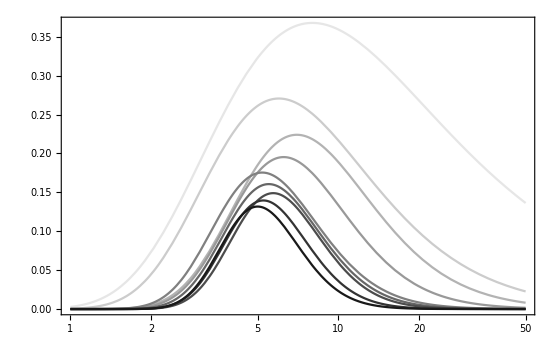

```mathematica
LogLinearPlot[Evaluate[Table[1/(i) 1 /(i-1)!(#[[i]]/tau)^i Exp[-#[[i]]/tau],{i,1,Length@#}]&@{8,12,21,25,26,33,40,42,45}],{tau,1,50},PlotStyle->GrayLevel/@Range[.9,0,-.1],Frame->True]
```

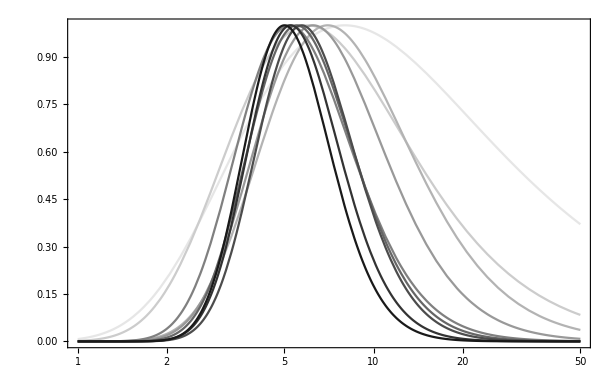

```mathematica
LogLinearPlot[Evaluate[Table[1/((ⅇ^-i i^i)/Gamma[i]) 1 /(i-1)!(#[[i]]/tau)^i Exp[-#[[i]]/tau],{i,1,Length@#}]&@{8,12,21,25,26,33,40,42,45}],{tau,1,50},PlotStyle->GrayLevel/@Range[.9,0,-.1],Frame->True]
```

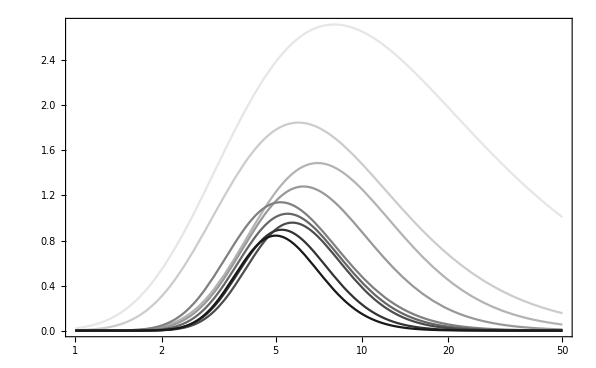

```mathematica
LogLinearPlot[Evaluate[Table[1/((ⅇ^-i i^i)/Gamma[i])^2 1 /(i-1)!(#[[i]]/tau)^i Exp[-#[[i]]/tau],{i,1,Length@#}]&@{8,12,21,25,26,33,40,42,45}],{tau,1,50},PlotStyle->GrayLevel/@Range[.9,0,-.1],Frame->True]
```

```mathematica
D[1 /(i-1)!(t/tau)^i Exp[-t/tau],tau]==0//FullSimplify
```

i==t/tau

```mathematica
1 /(i-1)!(t/tau)^i Exp[-t/tau]/.tau->(t/i)//FullSimplify
```

(ⅇ^-i i^i)/Gamma[i]

```mathematica
Limit[(ⅇ^-i i^i Sqrt[2Pi])/(Sqrt[i]Gamma[i]),i->1]
```

(√(2 π))/ⅇ

```mathematica
%//N
```

0.922137

```mathematica
1-%59^2
```

1-(2 π)/ⅇ^2

```mathematica
%//N
```

0.149663

```mathematica
1/E^2.
```

0.135335

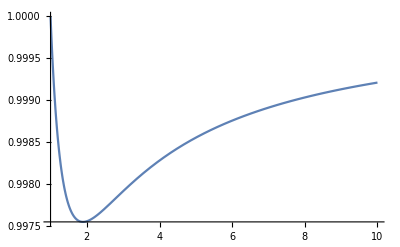

```mathematica
Plot[(ⅇ^-i i^i Sqrt[2Pi])/(Sqrt[i-(1-(2 π)/ⅇ^2)]Gamma[i]),{i,1,10},PlotRange->All]
```

```mathematica
Log[(1/tau)^i Exp[-t/tau]]/.tau->Exp[l]//FullSimplify
```

-i l-ⅇ^-l t

```mathematica
$Assumptions=l>0&&t>0&&i>0
```

l>0&&t>0&&i>0

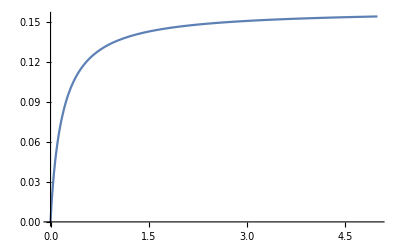

```mathematica
Plot[((ⅇ^-i i^i)/Gamma[i])^2/i,{i,0,5},PlotRange->All]
```

```mathematica
NSolve[1-Exp[-x]==.95,x]
```

{{x→2.99573}}